```mathematica
(*------ Change to won directory-----*)
SetDirectory["~/Dropbox/Sara/GeneralModel"];
(*-----------------------------------*)

(*------ Make parameter file-----*)
pa=Flatten[{set=1 ,index=1,NumPat=20,recpat=1, interval=1,tstart=0,maxT=1000,recfreq=50,recstart=0,recend=10000,NumRuns=1,drivertime=200,driverstart=0,driverend=300,NumDriver=10000,NumDriverPat=20,muJ=0.05,muA=0.125,d=0.001,gamma=(1-0.95)/2,beta=100,theta=9,ξ=0.5,ef=0.95,Ld=0.1,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=100000,meanTL=15,LarvProbs=Join[ConstantArray[0,10],ConstantArray[0.1,10]],U=1,centrad=1}];
Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""];
(*-----------------------------------*)
```

```mathematica
(*----------run the compiled code 'test' with the parameter fiel as input; put 'cout' output into cout-------*)
(*------------NB might be different syntax to run compiled code in windows-----------------------------------*)
cout=Import["!./test<Par1.csv","Table"];

(*---- in Windows I believe the line is this: ----------
cout=Import["!test.exe Par1.csv","Table"]
-----------------------------------*)


(*-----------------------------------------------------------------------------------------------------------*)
(*------------------import the 'Totals..' output file with numbers of males in each genotype------------------*)
totals=Import["Totals1run1.txt","Table"];
(*-----------------------------------------------------------------------------------------------------------*)
```

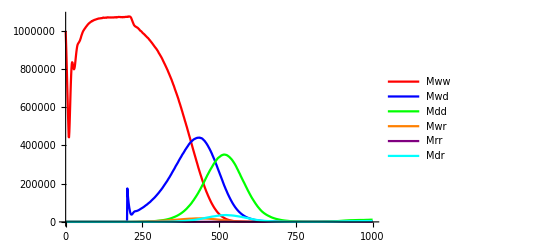

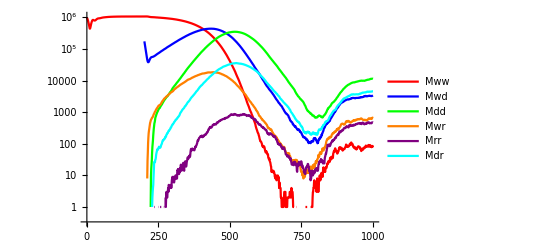

```mathematica
(*-------plot the output, both with arithmetic and log y-axis scale----------------------------------------*)
colours={Red,Blue,Green,Orange,Purple,Cyan};
ListLinePlot[Table[totals[[All,{1,i}]],{i,2,7,1}],PlotRange->All,PlotStyle->colours,PlotLegends->{"Mww","Mwd","Mdd","Mwr","Mrr","Mdr"}]
ListLogPlot[Table[totals[[All,{1,i}]],{i,2,7,1}],PlotRange->All,PlotStyle->colours,Joined->True,PlotLegends->{"Mww","Mwd","Mdd","Mwr","Mrr","Mdr"}]
(*-----------------------------------------------------------------------------------------------------------*)
```